## Answer 1

```mathematica
DSolve[θ''[t]+θ[t]+3 θ'[t]==0,θ[t],t]
```

{{θ[t]→ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}

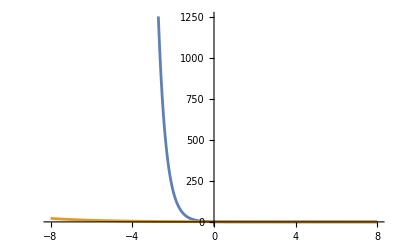

```mathematica
"plot linear components"{{θ[t]->ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}Plot[Evaluate[Cases[{{θ[t]->ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}⟦1,1,2⟧,a___ _C b___:>a b]],{t,-8,8}]
```

```mathematica
θ[t_]:=ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2](*Convert solution to function*)
```

```mathematica
θ[t]/.{{θ[t]->ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}(*Apply rules to variable in Mathematica;s language*)
```

{ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}

```mathematica
Simplify[{{θ[t]->ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}](*Just in a simplified form*)
```

{{ⅇ^(-1/2 (3+√5) t) (C[1]+ⅇ^(√5 t) C[2])→ⅇ^(-1/2 (3+√5) t) (C[1]+ⅇ^(√5 t) C[2])}}

```mathematica
{{θ[t]->ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}⟦1,1,2⟧(*Get solution*)
```

ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]

```mathematica
ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]/.{C[1]->1,C[2]->1}(*Set parameters*)
```

ⅇ^((-3/2-(√5)/2) t)+ⅇ^((-3/2+(√5)/2) t)

Answer 2

```mathematica
Solution1=DSolve[{x''[t]==-x[t]-x'[t],x[0]==1,x'[0]==0},x[t],t]
```

{{x[t]→1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])}}

```mathematica
(*M1: Looks straight but dont use in plot directly, use evaluate or others*)
x[t]/.Solution1[[1]]
```

1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])

```mathematica
(*M2*)
DSolve[{x''[t]==-x[t]-x'[t],x[0]==1,x'[0]==0},x[t],t]⟦1,1,2⟧
```

1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])

```mathematica
(*M3*)
x[t]/. First@DSolve[{x''[t]==-x[t]-x'[t],x[0]==1,x'[0]==0},x[t],t]
```

1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])

```mathematica
(*M4*)
Evaluate[x[t]/. Solution1[[1]]]
```

1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])

```mathematica
Plot[Evaluate[x[t]/. Solution1[[1]]],{t,0,10},PlotLabels->"x[t]",PlotStyle->Thick]
```

-Graphics-

Answer 3

```mathematica
DSolve[{x'[t]==-x[t] t,x[0]==1
},x[t],t]⟦1,1,2⟧
```

ⅇ^(-t^2/2)

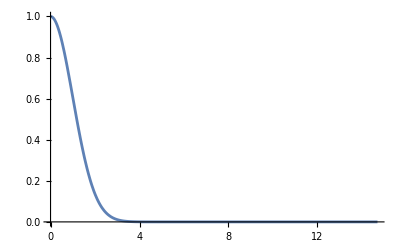

```mathematica
Plot[ⅇ^(-t^2/2),{t,0,14.696938456699069},PlotRange->Full]
```

## Answer 4

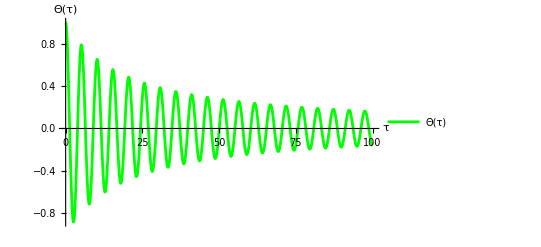

```mathematica
κ=0.5(*Dimensionless temprature*);
μ=0.1(*h*);

(*Solve the equation*)
sol=NDSolve[{Θ''[τ]==-(1+κ) Θ[τ]-μ Abs[Θ'[τ]] Θ'[τ],Θ[0]==1,Θ'[0]==0},Θ,{τ,0,100}];

(*Define the solution for easier reference*)
solExpr=Θ[τ]/. sol[[1]];

(*Plot the solution with enhanced styling*)
Plot[Evaluate[solExpr],{τ,0,100},PlotStyle->{Green},AxesLabel->{"τ","Θ(τ)"},LabelStyle->Directive[Bold,14],PlotLegends->Placed[{Style[TraditionalForm[Θ[τ]],Bold]},Top],PlotRange->All]
```